### Start choosing the example:

```mathematica
t=12;
beta = 0;
A = 0.2;
g[x]
```

Log[x]

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,1,0},{0,0,1,1},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->8,U1->0}];//Timing
```

DataToEquations: Triangle inequalities for switching costs: {}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: The system is:
NonNegative[8-j884+j885-j887+jt897+jt910+jt913]&&NonNegative[j884]&&NonNegative[j885]&&NonNegative[8-j887+j894+jt917]&&NonNegative[j887]&&NonNegative[jt897]&&NonNegative[j885-j887+jt910+jt913]&&NonNegative[j884+j894-jt910-jt913]&&NonNegative[jt917]&&NonNegative[j894]&&NonNegative[jt897]&&NonNegative[j885-j887+jt910+jt913]&&NonNegative[8-j884+jt897]&&NonNegative[j884-jt897]&&NonNegative[jt903]&&NonNegative[8-j884+j885-j887+jt897-jt903+jt910+jt913]&&NonNegative[j885+jt897-jt903-jt917]&&NonNegative[j884-j885+j894-jt897+jt903-jt910-jt913+jt917]&&NonNegative[-j885+jt903+jt917]&&NonNegative[j885-jt903]&&NonNegative[j884-jt910]&&NonNegative[jt910]&&NonNegative[j885-j887+jt910]&&NonNegative[j887-jt910]&&NonNegative[jt913]&&NonNegative[j894-jt913]&&NonNegative[j894]&&NonNegative[8-j887+jt917]&&NonNegative[jt917]&&NonNegative[j887-jt917]&&NonNegative[-u921+u922]&&NonNegative[u921-u922]&&NonNegative[u921-u927]&&NonNegative[u922-u927]&&NonNegative[8-j884+j885-j887+jt910+jt913-u921+u923]&&NonNegative[8-j884+j885-j887+jt910+jt913-u921+u924]&&NonNegative[-8+j884-j885+j887-jt910-jt913+u921-u923]&&NonNegative[-u923+u924]&&NonNegative[-8+j884-j885+j887-jt910-jt913+u921-u924]&&NonNegative[u923-u924]&&NonNegative[2 j884-2 j885+j887+j894-2 jt910-2 jt913-u922+u923]&&NonNegative[j884-j885+j887-jt910-jt913-u922+u925]&&NonNegative[-2 j884+2 j885-j887-j894+2 jt910+2 jt913+u922-u923]&&NonNegative[-j884+j885-j894+jt910+jt913-u923+u925]&&NonNegative[-j884+j885-j887+jt910+jt913+u922-u925]&&NonNegative[j884-j885+j894-jt910-jt913+u923-u925]&&NonNegative[8-2 j887+2 j894-u924+u925]&&NonNegative[8-j887+j894-u924]&&NonNegative[-8+2 j887-2 j894+u924-u925]&&NonNegative[j887-j894-u925]&&(jt897==0||8-j884+j885-j887+jt897+jt910+jt913==0)&&(j885-j887+jt910+jt913==0||j884==0)&&(j884+j894-jt910-jt913==0||j885==0)&&(jt917==0||8-j887+j894+jt917==0)&&(j894==0||j887==0)&&(jt897==0||j885-j887+jt910+jt913==0)&&(jt903==0||j885+jt897-jt903-jt917==0)&&(8-j884+j885-j887+jt897-jt903+jt910+jt913==0||-j885+jt903+jt917==0)&&(j884-j885+j894-jt897+jt903-jt910-jt913+jt917==0||j885-jt903==0)&&(j884-jt910==0||j885-j887+jt910==0)&&(jt910==0||jt913==0)&&(j887-jt910==0||j894-jt913==0)&&(j894==0||jt917==0)&&(jt897==0||-u921+u922==0)&&(j885-j887+jt910+jt913==0||u921-u922==0)&&(8-j884+jt897==0||u921-u927==0)&&(j884-jt897==0||u922-u927==0)&&(jt903==0||8-j884+j885-j887+jt910+jt913-u921+u923==0)&&(8-j884+j885-j887+jt897-jt903+jt910+jt913==0||8-j884+j885-j887+jt910+jt913-u921+u924==0)&&(j885+jt897-jt903-jt917==0||-8+j884-j885+j887-jt910-jt913+u921-u923==0)&&(j884-j885+j894-jt897+jt903-jt910-jt913+jt917==0||-u923+u924==0)&&(-j885+jt903+jt917==0||-8+j884-j885+j887-jt910-jt913+u921-u924==0)&&(j885-jt903==0||u923-u924==0)&&(j884-jt910==0||2 j884-2 j885+j887+j894-2 jt910-2 jt913-u922+u923==0)&&(jt910==0||j884-j885+j887-jt910-jt913-u922+u925==0)&&(j885-j887+jt910==0||-2 j884+2 j885-j887-j894+2 jt910+2 jt913+u922-u923==0)&&(j887-jt910==0||-j884+j885-j894+jt910+jt913-u923+u925==0)&&(jt913==0||-j884+j885-j887+jt910+jt913+u922-u925==0)&&(j894-jt913==0||j884-j885+j894-jt910-jt913+u923-u925==0)&&(j894==0||8-2 j887+2 j894-u924+u925==0)&&(8-j887+jt917==0||8-j887+j894-u924==0)&&(jt917==0||-8+2 j887-2 j894+u924-u925==0)&&(j887-jt917==0||j887-j894-u925==0)
and the rules are:
<|j883→8-j884+j885-j887+jt897+jt910+jt913,j886→8-j887+j894+jt917,j888→8,j889→8,j890→jt897,j891→j885-j887+jt910+jt913,j892→j884+j894-jt910-jt913,j893→jt917,j895→0,j896→0,jt898→0,jt899→j885-j887+jt910+jt913,jt900→0,jt901→8-j884+jt897,jt902→j884-jt897,jt904→8-j884+j885-j887+jt897-jt903+jt910+jt913,jt905→j885+jt897-jt903-jt917,jt906→j884-j885+j894-jt897+jt903-jt910-jt913+jt917,jt907→-j885+jt903+jt917,jt908→j885-jt903,jt909→j884-jt910,jt911→j885-j887+jt910,jt912→j887-jt910,jt914→j894-jt913,jt915→j894,jt916→8-j887+jt917,jt918→j887-jt917,jt919→0,jt920→0,u926→0,u928→-8+j884-j885+j887-jt910-jt913+u921,u929→-j884+j885-j887+jt910+jt913+u922,u930→j884-j885+j894-jt910-jt913+u923,u931→-8+j887-j894+u924,u932→-j887+j894+u925,u933→0,u934→u927|>

DataToEquations: It took 4.3487 seconds to reduce with NewReduce!

DataToEquations: After NewReduce, the system is:
j884==4&&j885==0&&j887==4&&j894==0&&jt897==0&&jt903==0&&jt910==4&&jt913==0&&jt917==0&&u921==8&&u922==8&&u923==4&&u924==4&&u925==4&&u927==8
and the rules are:
<|j883→8-j884+j885-j887+jt897+jt910+jt913,j886→8-j887+j894+jt917,j888→8,j889→8,j890→jt897,j891→j885-j887+jt910+jt913,j892→j884+j894-jt910-jt913,j893→jt917,j895→0,j896→0,jt898→0,jt899→j885-j887+jt910+jt913,jt900→0,jt901→8-j884+jt897,jt902→j884-jt897,jt904→8-j884+j885-j887+jt897-jt903+jt910+jt913,jt905→j885+jt897-jt903-jt917,jt906→j884-j885+j894-jt897+jt903-jt910-jt913+jt917,jt907→-j885+jt903+jt917,jt908→j885-jt903,jt909→j884-jt910,jt911→j885-j887+jt910,jt912→j887-jt910,jt914→j894-jt913,jt915→j894,jt916→8-j887+jt917,jt918→j887-jt917,jt919→0,jt920→0,u926→0,u928→-8+j884-j885+j887-jt910-jt913+u921,u929→-j884+j885-j887+jt910+jt913+u922,u930→j884-j885+j894-jt910-jt913+u923,u931→-8+j887-j894+u924,u932→-j887+j894+u925,u933→0,u934→u927|>

DataToEquations: Critical congestion solved.

all ok? up to here?

{j883-j890+IntM[j883-j890,1->2],j884-j891+IntM[j884-j891,1->3],j885-j892+IntM[j885-j892,2->3],j886-j893+IntM[j886-j893,2->4],j887-j894+IntM[j887-j894,3->4]}

DataToEquations: Done.

{4.73684,Null}

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→95.,u1096→95.,u1097→55.,u1098→55.,u1099→55.,u1100→15.,u1101→95.,u1102→55.,u1103→55.,u1104→55.,u1105→15.,u1106→15.,u1107→15.,u1108→95.|>

#### Graphs for critical congestion and same hamiltonian for each edge

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
```

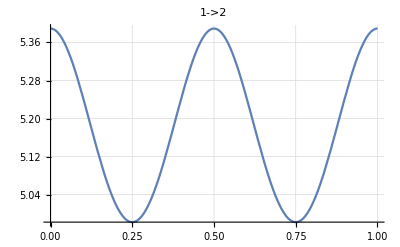
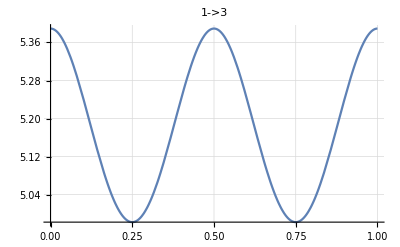
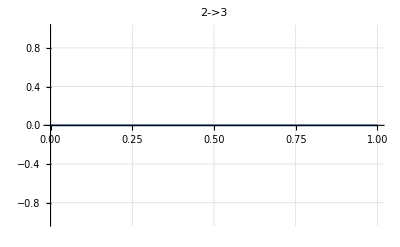
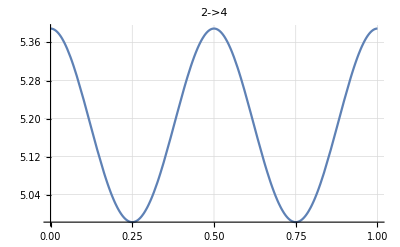
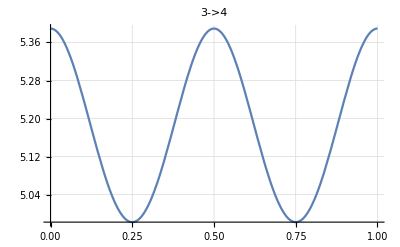

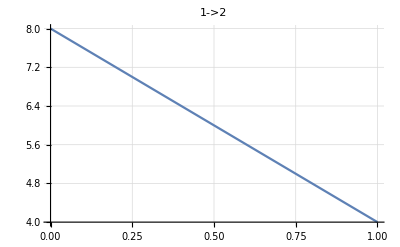
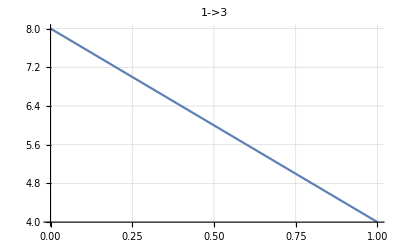
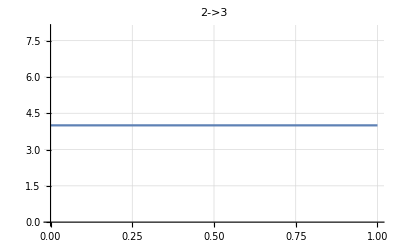

```mathematica
(*Don't forget to change the Range!*)
alpha =1;
FFR=MFGEquations["criticalreduced1"][[2]];
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->#,(*PlotRange->{-0.1,2.4},*)GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->#(*,PlotRange->{1-0.1,4.7}*),GridLines->Automatic]&/@MFGEquations["BEL"]
```

#### Graphs for critical congestion and different Hamiltonians on edges

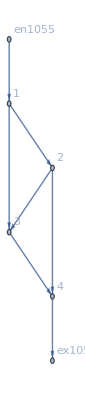

```mathematica
MFGEquations["FG"]
```

```mathematica
(*the hamiltonian that we define a posteriori needs to be consistent with the algebraic system provided by the current method.*)
```

```mathematica
H=Function[{x,p,m,edge},
Which[edge === 1->2 || edge === 3->4,
p^2/(2 m)+1-g[m],
edge === 1->3||edge===2->4,
p^2/(2 m)-g[m],
edge === 2->3,
x,
True,
40
]
];
```

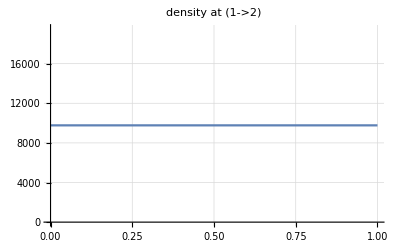
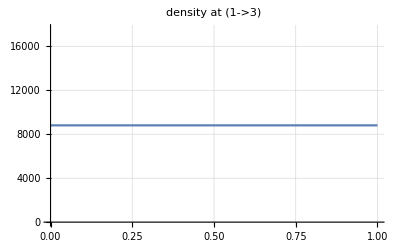
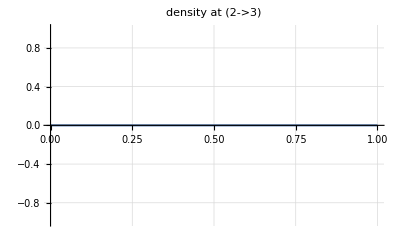
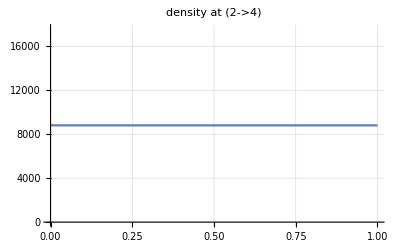
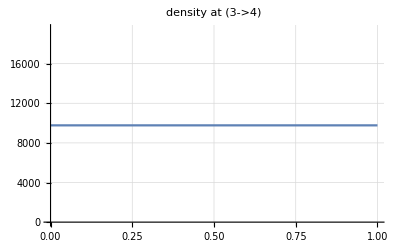

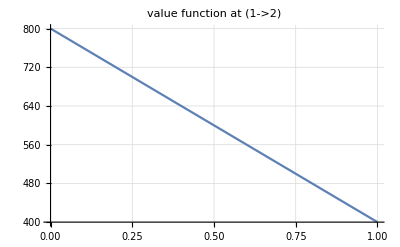
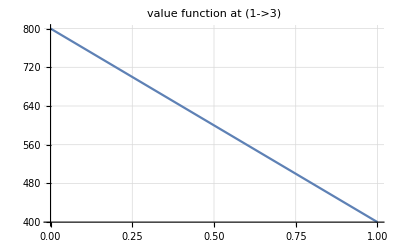
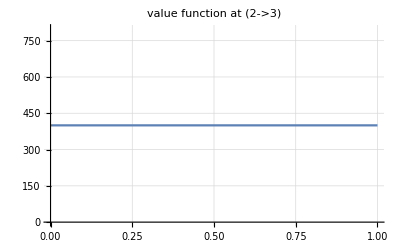

```mathematica
(*Don't forget to change the Range!*)
alpha =1;
FFR=MFGEquations["criticalreduced1"][[2]];
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"density at " #,(*PlotRange->{-0.3,160},*)GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"value function at " #,(*PlotRange->{15-0.1,100},*)GridLines->Automatic]&/@MFGEquations["BEL"]
```

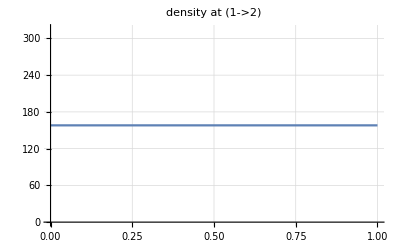
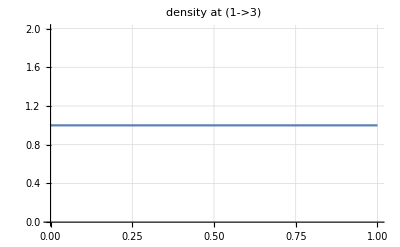
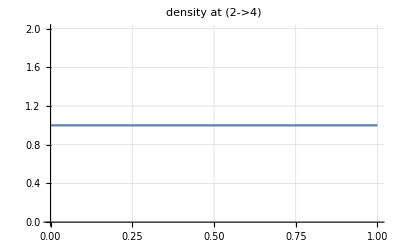
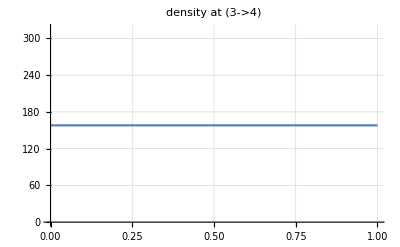
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

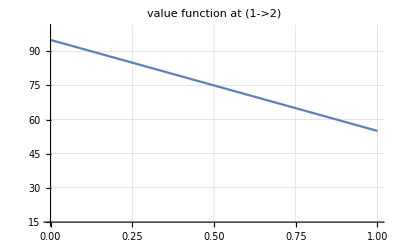
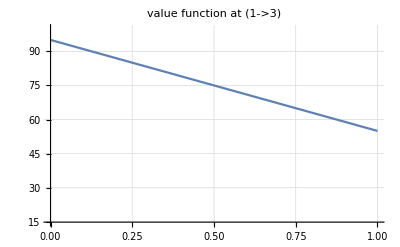
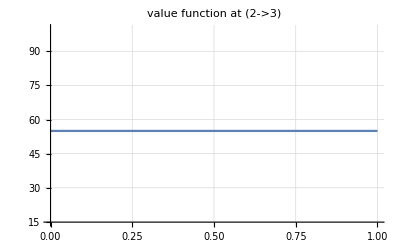
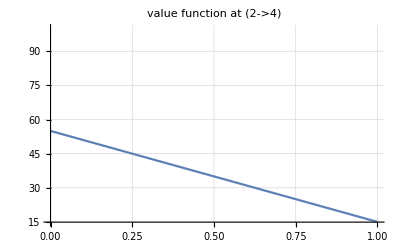
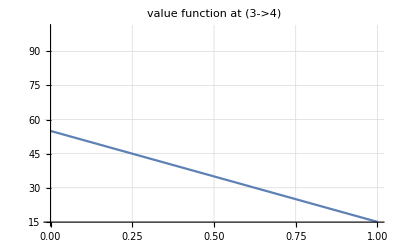

```mathematica
H=Function[{x,p,m,edge},
Which[edge === 1->2 || edge === 3->4,
p^2/(2 m)-g[m],
edge === 1->3||edge===2->4,
p^2/(2 m)g[m],
edge === 2->3,
p^2/(2 m)-100-m,
True,
40
]
];
(*Don't forget to change the Range!*)
alpha =1;
FFR=MFGEquations["criticalreduced1"][[2]];
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"density at " #,(*PlotRange->{-0.3,160},*)GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"value function at " #,PlotRange->{15-0.1,100},GridLines->Automatic]&/@MFGEquations["BEL"]
```

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.16139×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.16139×10^-16

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→19.6805,u1096→19.6805,u1097→17.3402,u1098→17.3402,u1099→17.3402,u1100→15.,u1101→19.6805,u1102→17.3402,u1103→17.3402,u1104→17.3402,u1105→15.,u1106→15.,u1107→15.,u1108→19.6805|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j557-j564-u595+u602==38.3971&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.272367

FRX1: nonlinear: 
j557-j564-u595+u602==52.7699&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0925456

FRX1: nonlinear: 
j557-j564-u595+u602==58.1516&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0334946

FRX1: nonlinear: 
j557-j564-u595+u602==60.1668&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0123877

FRX1: nonlinear: 
j557-j564-u595+u602==60.9215&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00461755

FRX1: nonlinear: 
j557-j564-u595+u602==61.2041&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00172622

FRX1: nonlinear: 
j557-j564-u595+u602==61.3099&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000646026

FRX1: nonlinear: 
j557-j564-u595+u602==61.3496&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000241869

FRX1: nonlinear: 
j557-j564-u595+u602==61.3644&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000905682

FRX1: nonlinear: 
j557-j564-u595+u602==61.37&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000339154

<|j557→63.0137,j558→16.9863,j559→15.3425,j560→47.6712,j561→32.3288,j562→80,j563→80,j564→0.,j565→0,j566→0,j567→0,j568→0,j569→0,j570→0,jt571→0.,jt572→0,jt573→0,jt574→0,jt575→63.0137,jt576→16.9863,jt577→15.3425,jt578→47.6712,jt579→0.,jt580→0.,jt581→0,jt582→0,jt583→0,jt584→16.9863,jt585→0,jt586→15.3425,jt587→0,jt588→0,jt589→0,jt590→47.6712,jt591→0,jt592→32.3288,jt593→0,jt594→0,u595→64.315,u596→64.315,u597→62.6712,u598→62.6712,u599→47.3288,u600→15,u601→64.315,u602→62.6712,u603→47.3288,u604→47.3288,u605→15.,u606→15.,u607→15,u608→64.315|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.42094×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.42094×10^-17

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→23.1887,u1096→23.1887,u1097→19.0944,u1098→19.0944,u1099→19.0944,u1100→15.,u1101→23.1887,u1102→19.0944,u1103→19.0944,u1104→19.0944,u1105→15.,u1106→15.,u1107→15.,u1108→23.1887|>

FRX1: nonlinear: 
j883-j890-u921+u928==0.561845&&j884-j891-u922+u929==0.561845&&j885-j892-u923+u930==0&&j886-j893-u924+u931==0.561845&&j887-j894-u925+u932==0.561845

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.90412×10^-16

FRX1: nonlinear: 
j883-j890-u921+u928==0.561845&&j884-j891-u922+u929==0.561845&&j885-j892-u923+u930==0&&j886-j893-u924+u931==0.561845&&j887-j894-u925+u932==0.561845

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.90412×10^-16

<|j883→4.,j884→4.,j885→0.,j886→4.,j887→4.,j888→8,j889→8,j890→0.,j891→0,j892→0,j893→0,j894→0,j895→0,j896→0,jt897→0.,jt898→0,jt899→0,jt900→0,jt901→4.,jt902→4.,jt903→0.,jt904→4.,jt905→0.,jt906→0.,jt907→0,jt908→0,jt909→0,jt910→4.,jt911→0,jt912→0.,jt913→0,jt914→0,jt915→0,jt916→4.,jt917→0,jt918→4.,jt919→0,jt920→0,u921→6.87631,u922→6.87631,u923→3.43815,u924→3.43815,u925→3.43815,u926→0,u927→6.87631,u928→3.43815,u929→3.43815,u930→3.43815,u931→0.,u932→0.,u933→0,u934→6.87631|>

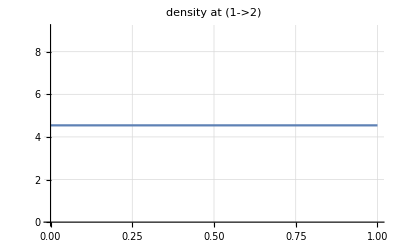
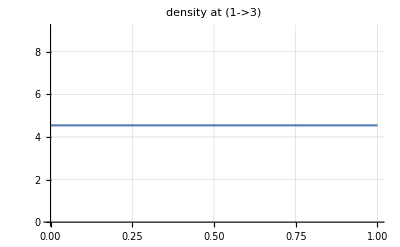
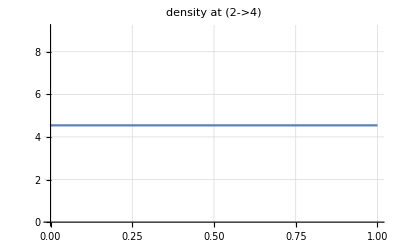
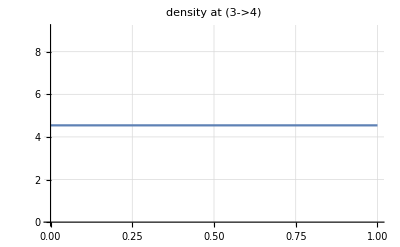
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

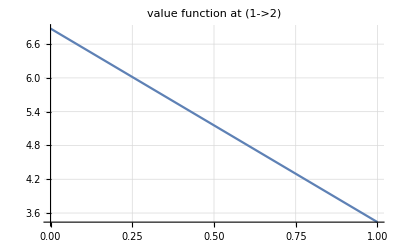
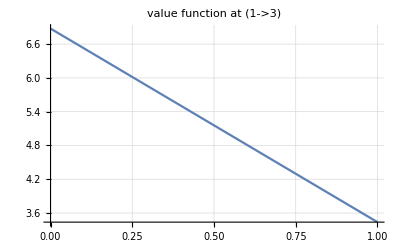
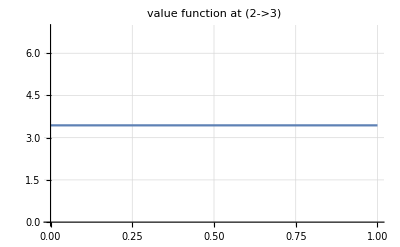
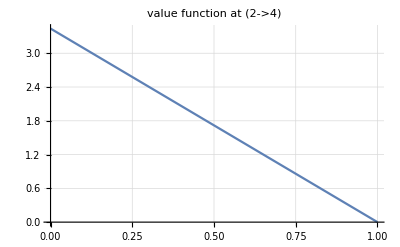
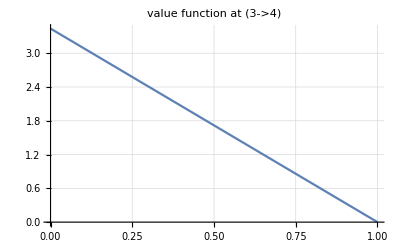

```mathematica
alpha = 0.9;
H=Function[{x,p,m,edge},
Which[edge === 1->2 || edge === 3->4,
p^2/(2 m^alpha)-g[m],
edge === 1->3||edge===2->4,
p^2/(2 m^alpha)-g[m],
edge === 2->3,
p^2/(2 m^alpha)+10-g[m],
True,
40
]
];
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"density at " #,(*PlotRange->{-0.3,160},*)GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"value function at " #,(*PlotRange->{15-0.1,100},*)GridLines->Automatic]&/@MFGEquations["BEL"]
```

FRX1: nonlinear: 
j883-j890-u921+u928==0.574963&&j884-j891-u922+u929==0.574963&&j885-j892-u923+u930==0&&j886-j893-u924+u931==0.574963&&j887-j894-u925+u932==0.574963

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.72378×10^-16

FRX1: nonlinear: 
j883-j890-u921+u928==0.574963&&j884-j891-u922+u929==0.574963&&j885-j892-u923+u930==0&&j886-j893-u924+u931==0.574963&&j887-j894-u925+u932==0.574963

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.72378×10^-16

<|j883→4.,j884→4.,j885→0.,j886→4.,j887→4.,j888→8,j889→8,j890→0.,j891→0,j892→0,j893→0,j894→0,j895→0,j896→0,jt897→0.,jt898→0,jt899→0,jt900→0,jt901→4.,jt902→4.,jt903→0.,jt904→4.,jt905→0.,jt906→0.,jt907→0,jt908→0,jt909→0,jt910→4.,jt911→0,jt912→0.,jt913→0,jt914→0,jt915→0,jt916→4.,jt917→0,jt918→4.,jt919→0,jt920→0,u921→6.85007,u922→6.85007,u923→3.42504,u924→3.42504,u925→3.42504,u926→0,u927→6.85007,u928→3.42504,u929→3.42504,u930→3.42504,u931→0.,u932→0.,u933→0,u934→6.85007|>

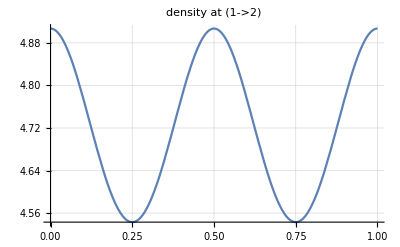
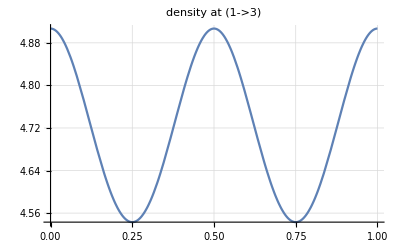
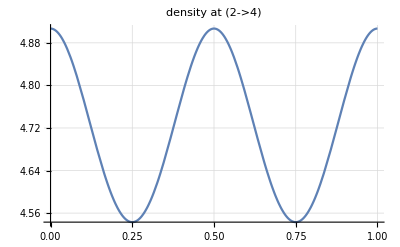
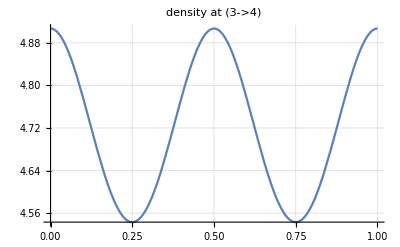
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

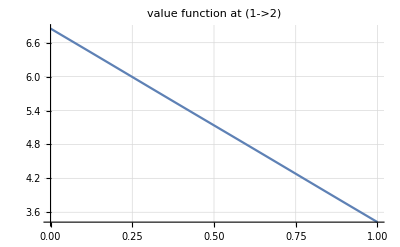
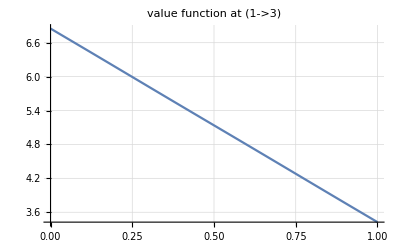
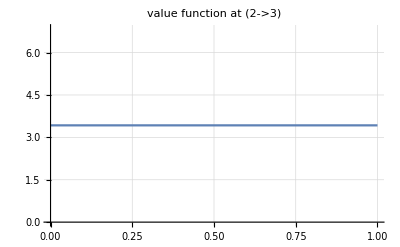
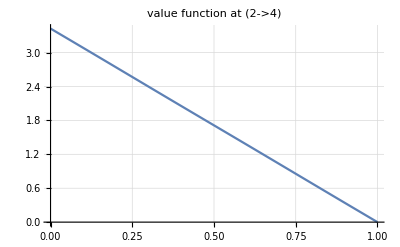
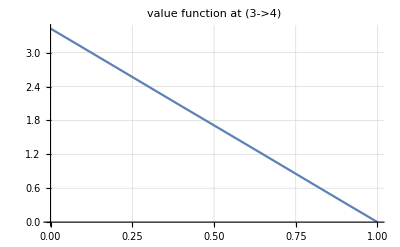

```mathematica
alpha = 0.9;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"]
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"density at " #,(*PlotRange->{-0.3,160},*)GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"value function at " #,(*PlotRange->{15-0.1,100},*)GridLines->Automatic]&/@MFGEquations["BEL"]
```

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j557-j564-u595+u602==0&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[8.52651×10^-14,ComplexInfinity]

<|j557→40,j558→40,j559→0,j560→40,j561→40,j562→80,j563→80,j564→0,j565→0,j566→0,j567→0,j568→0,j569→0,j570→0,jt571→0,jt572→0,jt573→0,jt574→0,jt575→40,jt576→40,jt577→0,jt578→40,jt579→0,jt580→0,jt581→0,jt582→0,jt583→0,jt584→40,jt585→0,jt586→0,jt587→0,jt588→0,jt589→0,jt590→40,jt591→0,jt592→40,jt593→0,jt594→0,u595→95,u596→95,u597→55,u598→55,u599→55,u600→15,u601→95,u602→55,u603→55,u604→55,u605→15,u606→15,u607→15,u608→95|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j557-j564-u595+u602==-178.622&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.52706

FRX1: nonlinear: 
j557-j564-u595+u602==94.1437&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.19236

FRX1: nonlinear: 
j557-j564-u595+u602==-489.411&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.36457

FRX1: nonlinear: 
j557-j564-u595+u602==1342.45&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.12903

FRX1: nonlinear: 
j557-j564-u595+u602==-10403.8&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.05112

FRX1: nonlinear: 
j557-j564-u595+u602==203499.&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.01121

FRX1: nonlinear: 
j557-j564-u595+u602==-1.81556×10^7&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00118

FRX1: nonlinear: 
j557-j564-u595+u602==1.53451×10^10&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00004

FRX1: nonlinear: 
j557-j564-u595+u602==-3.77223×10^14&&j558-j565-u596+u603==6.67572×10^-6&&j559-j566-u597+u604==-3.8147×10^-6&&j560-j567-u598+u605==-2.14577×10^-6&&j561-j568-u599+u606==2.14577×10^-6

FRX1: The last system in the iteration was inconsistent.
Returning the last feasible solution.

FRX1: nonlinear: 
j557-j564-u595+u602==-3.77223×10^14&&j558-j565-u596+u603==6.67572×10^-6&&j559-j566-u597+u604==-3.8147×10^-6&&j560-j567-u598+u605==-2.14577×10^-6&&j561-j568-u599+u606==2.14577×10^-6

FRX1: The last system in the iteration was inconsistent.
Returning the last feasible solution.

```mathematica
<|j557->5.754412314431864*^9,j558->0.,j559->3.8362748496212425*^9,j560->1.9181374648106213*^9,ej561->0.,j562->80,j563->80,j564->0.,j565->5.754412234431864*^9,j566->0,j567->0,j568->1.9181373848106213*^9,j569->0,j570->0,jt571->0.,jt572->0,jt573->5.754412234431864*^9,jt574->0,jt575->80.,jt576->0.,jt577->3.8362748496212425*^9,jt578->1.9181374648106213*^9,jt579->0.,jt580->0.,jt581->0,jt582->0,jt583->0.,jt584->0.,jt585->3.8362748496212425*^9,jt586->0.,jt587->1.9181373848106213*^9,jt588->0.,jt589->1.9181373848106213*^9,jt590->80.,jt591->0,jt592->0.,jt593->0,jt594->0,u595->-7.672549604242487*^9,u596->-7.672549604242487*^9,u597->1.9181374798106213*^9,u598->1.9181374798106213*^9,u599->-1.9181373698106213*^9,u600->15,u601->-7.672549604242487*^9,u602->1.9181374798106213*^9,u603->-1.9181373698106232*^9,u604->-1.9181373698106232*^9,u605->15.,u606->15.,u607->15,u608->-7.672549604242487*^9|>
```

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→7208.19,u1096→7208.19,u1097→3611.59,u1098→3611.59,u1099→3611.59,u1100→15.,u1101→7208.19,u1102→3611.59,u1103→3611.59,u1104→3611.59,u1105→15.,u1106→15.,u1107→15.,u1108→7208.19|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→2.99468×10^14,u1096→2.99468×10^14,u1097→1.49734×10^14,u1098→1.49734×10^14,u1099→1.49734×10^14,u1100→15.,u1101→2.99468×10^14,u1102→1.49734×10^14,u1103→1.49734×10^14,u1104→1.49734×10^14,u1105→15.,u1106→15.,u1107→15.,u1108→2.99468×10^14|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.707107

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«5 more identical outputs»

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.707107

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«5 more identical outputs»

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→95.,u1096→95.,u1097→55.,u1098→55.,u1099→55.,u1100→15.,u1101→95.,u1102→55.,u1103→55.,u1104→55.,u1105→15.,u1106→15.,u1107→15.,u1108→95.|>